```mathematica
(* ΑΡΙΘΜΗΤΙΚΗ ΛΥΣΗ ΤΟΥ ΑΡΜΟΝΙΚΟΥ ΤΑΛΑΝΤΩΤΗ *)
```

```mathematica
Clear["Global`*"]
```

d=0.

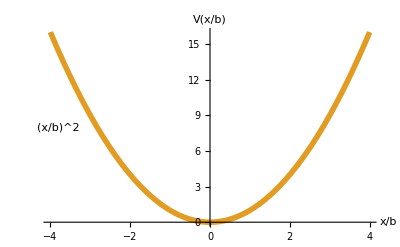

```mathematica
d=0.0;(* d / lambda ΕΙΝΑΙ Ο ΒΑΘΜΟΣ ΑΝΑΡΜΟΝΙΚΟΤΗΤΑΣ *)
Print[" d=",d]
v[xi_]:=xi^2 + d*xi^4;
Plot[{xi^2, v[xi]}, {xi, -4, 4},AxesStyle -> AbsoluteThickness[1], AxesLabel->{"x/b","V(x/b)"},PlotStyle->{ Dashing[{0.05,0.05}],Thickness[0.01]  },Epilog->{Text[StyleForm["(x/b)^2"], {-3.8, 8}] ,Text[StyleForm["(x/b)^2 + d*(x/b)^4"], {3,18}]  }   ]
```

```mathematica
xiend=4.;
(* ΕΠΙΛΥΣΗ ΜΕ NDSolve ΓΙΑ ΑΡΤΙΕΣ ΣΥΝΑΡΤΗΣΕΙΣ *)
u1even[e_]:=NDSolve[ { D[u[xi], {xi,2}] +(e-v[xi])*u[xi]==0,u[0]==1,u'[0]==0 }, u, {xi, 0,xiend}   ]
(* ΕΠΙΛΥΣΗ ΜΕ NDSolve ΓΙΑ ΠΕΡΙΤΤΕΣ ΣΥΝΑΡΤΗΣΕΙΣ *)
u1odd[e_]:=NDSolve[ { D[u[xi], {xi,2}] +(e-v[xi])*u[xi]==0,u[0]==0,u'[0]==1 }, u, {xi, 0,xiend}   ]
(* ΜΗ ΚΑΝΟΝΙΚΟΠΟΙΗΜΕΝΗ ΑΡΤΙΑ ΛΥΣΗ ΤΗΣ ΔΙΑΦΟΡΙΚΗΣ ΕΞΙΣΩΣΗΣ *)
u2even[e_,xi_]:= u[xi]/.Flatten[ u1even[e] ]
u2odd[e_,xi_]:= u[xi]/.Flatten[ u1odd[e] ]
(* ΠΑΡΑΓΟΝΤΑΣ ΚΑΝΟΝΙΚΟΠΟΙΗΣΗΣ *)
normeven[e_]:=Sqrt[2*NIntegrate[ Evaluate[u2even[e,xi]^2],{xi,0,xiend}]  ];
normodd[e_]:=Sqrt[2*NIntegrate[ Evaluate[u2odd[e,xi]^2],{xi,0,xiend}]  ];
(* ΚΑΝΟΝΙΚΟΠΟΙΗΜΕΝΗ ΛΥΣΗ *)
ueven[e_,xi_]:=   Which[xi>=0, u2even[e,xi]/normeven[e],xi<0,  u2even[e,-xi]/normeven[e]];
uodd[e_,xi_]:=   Which[xi>=0, u2odd[e,xi]/normodd[e],xi<0,  u2odd[e,-xi]/normodd[e]];
```

```mathematica
(* ΒΛΕΠΟΥΜΕ ΤΗΝ ΣΥΜΠΕΡΙΦΟΡΑ ΓΙΑ ΤΡΕΙΣ "ΤΥΧΑΙΕΣ" ΤΙΜΕΣ ΤΗΣ ΕΝΕΡΓΕΙΑΣ *)
```

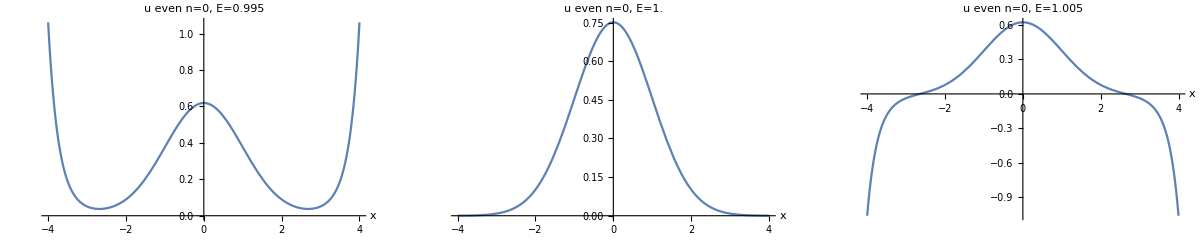

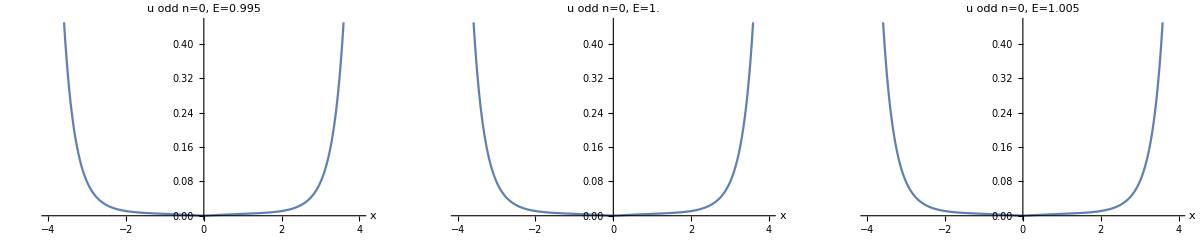

```mathematica
eeeRandom={0.995, 1., 1.005}; 
fig=Table[Null,{3}];
Do[fig[[i]] = Plot[ ueven[eeeRandom[[i]],x] , {x,-xiend,xiend}, DisplayFunction->Identity,
AxesLabel->{"x", "          u even n=0,"StringForm[ "E=``",eeeRandom[[i]]," "]}     
 ], {i,1,3} ]
figRandom= GraphicsGrid[{{fig[[1]],fig[[2]],fig[[3]] } } ];
Show[figRandom, $DisplayFunction-> DisplayFunction ]

fig=Table[Null,{3}];
Do[fig[[i]] = Plot[ uodd[eeeRandom[[i]],x] , {x,-xiend,xiend}, DisplayFunction->Identity,
AxesLabel->{"x", "          u odd n=0,"StringForm[ "E=``",eeeRandom[[i]]," "]}     
 ], {i,1,3} ]
figRandom= GraphicsGrid[{{fig[[1]],fig[[2]],fig[[3]] } } ];
Show[figRandom, $DisplayFunction-> DisplayFunction ]
```

```mathematica
(* ΧΡΗΣΙΜΟΠΟΙΟΥΜΕ ΤΗ ΜΕΘΟΔΟ ΤΗΣ ΔΙΠΛΗΣ ΑΝΑΖΗΤΗΣΗΣ ΠΟΥ ΕΧΕΙ ΑΝΑΦΕΡΘΕΙ ΚΑΙ ΣΤΟ SECTION 1.5.2 *)
```

```mathematica
uevenInf[e_]:=ueven[e,xi]/.xi->xiend;
{ eeven=Table[Null,{20}]};(* ΨΑΧΝΟΥΜΕ ΙΔΙΟΤΙΜΕΣ ΓΙΑ ΑΡΤΙΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
{istate=3,  step1=0.05,istep1=IntegerPart[ 20/step1]};
uoddInf[e_]:=uodd[e,xi]/.xi->xiend;
{ eodd=Table[Null,{20}]};(* ΨΑΧΝΟΥΜΕ ΙΔΙΟΤΙΜΕΣ ΓΙΑ ΠΕΡΤΤΤΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
{istate=3,  step1=0.05,istep1=IntegerPart[ 20/step1]};
```

```mathematica
{ex=0,  esave=0};
Do[                             (* ITERATIONS ΓΙΑ ΤΙΣ ΔΙΑΦΟΡΕΣ ΚΑΤΑΣΤΑΣΕΙΣ  *)
 ex=ex+step1;
Do[                        (* ITERATIONS ΓΙΑ ΤΙΣ ΔΙΑΦΟΡΕΣ ΕΝΕΡΓΕΙΕΣ ΓΙΑ ΜΙΑ ΚΑΤΑΣΤΑΣΗ *)
test=Chop[ Evaluate[  uevenInf[ex]  ]  ];  testsign=Sign[test];
(* Print["e[",i2,"]=",ex," test= ",test," sign=", testsign ," ",savesign];  *)
If[test==0, Break[] ];
If[i2==1, savesign=testsign];
If[testsign==savesign,
 {savesign=testsign,savetest=test,esave=ex,ex=ex+step1},    
     Break[]      ]     ,
 {i2,1,istep1}]; (* END OF ITERATIONS ΓΙΑ ΤΙΣ ΔΙΑΦΟΡΕΣ ΕΝΕΡΓΕΙΕΣ ΓΙΑ ΜΙΑ ΚΑΤΑΣΤΑΣΗ  *)

b=(savetest-test)/(esave-ex);
a=savetest-b*esave;
eeven[[i1]]=-a/b;   ex=-a/b;
test=Chop[ Evaluate[  uevenInf[ex]  ]  ];  
Print["eeven[",i1,"]=",ex," test=",test]

,{i1,1,istate}];  (* END OF ITERATIONS ΓΙΑ ΤΙΣ ΔΙΑΦΟΡΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

eeven[1]=1.00001 test=-0.0014304

eeven[2]=5.00043 test=0.000424128

eeven[3]=9.01929 test=-0.0000202863

```mathematica
{ex=0,  esave=0};
Do[                             (* ITERATIONS ΓΙΑ ΤΙΣ ΔΙΑΦΟΡΕΣ ΚΑΤΑΣΤΑΣΕΙΣ  *)
 ex=ex+step1;
Do[                        (* ITERATIONS ΓΙΑ ΤΙΣ ΔΙΑΦΟΡΕΣ ΕΝΕΡΓΕΙΕΣ ΓΙΑ ΜΙΑ ΚΑΤΑΣΤΑΣΗ *)
test=Chop[ Evaluate[  uoddInf[ex]  ]  ];  testsign=Sign[test];
(* Print["e[",i2,"]=",ex," test= ",test," sign=", testsign ," ",savesign];  *)
If[test==0, Break[] ];
If[i2==1, savesign=testsign];
If[testsign==savesign,
 {savesign=testsign,savetest=test,esave=ex,ex=ex+step1},    
     Break[]      ]     ,
 {i2,1,istep1}]; (* END OF ITERATIONS ΓΙΑ ΤΙΣ ΔΙΑΦΟΡΕΣ ΕΝΕΡΓΕΙΕΣ ΓΙΑ ΜΙΑ ΚΑΤΑΣΤΑΣΗ  *)

b=(savetest-test)/(esave-ex);
a=savetest-b*esave;
eodd[[i1]]=-a/b;   ex=-a/b;
test=Chop[ Evaluate[  uoddInf[ex]  ]  ];  
Print["eodd[",i1,"]=",ex," test=",test]

,{i1,1,istate}];  (* END OF ITERATIONS ΓΙΑ ΤΙΣ ΔΙΑΦΟΡΕΣ ΚΑΤΑΣΤΑΣΕΙΣ *)
```

eodd[1]=3.00005 test=-0.000976845

eodd[2]=7.00342 test=0.000173675

eodd[3]=11.0788 test=2.32989×10^-7

```mathematica
(* ΓΡΑΦΙΚΗ ΑΠΕΙΚΟΝΙΣΗ ΚΑΙ ΣΥΓΚΡΙΣΗ ΜΕ ΘΕΩΡΗΤΙΚΕΣ ΤΙΜΕΣ *)
```

```mathematica
eevenTh={1,5,9}; 
eoddTh={2,6,10};
```

eeven[1]=1.00001  DE=6.52201×10^-6  norm=1.

eeven[2]=5.00043  DE=0.000433333  norm=1.

eeven[3]=9.01929  DE=0.0192911  norm=1.

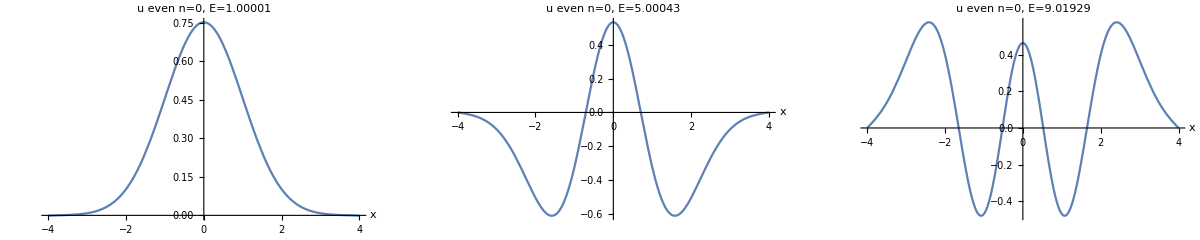

```mathematica
fig=Table[Null,{3}];
Do[{DEeven=eeven[[i]]-eevenTh[[i]],
intev=2*NIntegrate[Evaluate[ueven[eeven[[i]],x]^2 ],{x,0,xiend}],
Print["eeven[",i,"]=",eeven[[i]],"  DE=", DEeven,"  norm=",intev  ] ,
fig[[i]] = Plot[ ueven[eeven[[i]],x] , {x,-xiend,xiend}, DisplayFunction->Identity,
AxesLabel->{"x", "          u even n=0,"StringForm[ "E=``",eeven[[i]]," "]}     
 ]}, {i,1,istate} ]
figNum= GraphicsGrid[{{fig[[1]],fig[[2]],fig[[3]] } } ];
Show[figNum, $DisplayFunction-> DisplayFunction ]
```

eeven[1]=3.00005  DE=1.00005  norm=1.

eeven[2]=7.00342  DE=1.00342  norm=1.

eeven[3]=11.0788  DE=1.07884  norm=1.

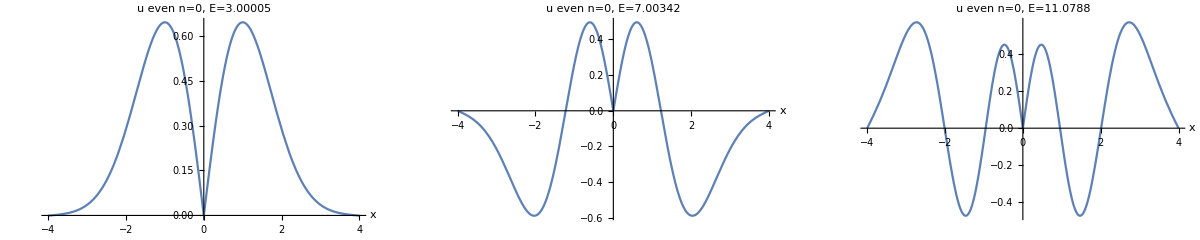

```mathematica
fig=Table[Null,{3}];
Do[{DOdd=eodd[[i]]-eoddTh[[i]],
intev=2*NIntegrate[Evaluate[uodd[eodd[[i]],x]^2 ],{x,0,xiend}],
Print["eeven[",i,"]=",eodd[[i]],"  DE=", DOdd,"  norm=",intev  ] ,
fig[[i]] = Plot[ uodd[eodd[[i]],x] , {x,-xiend,xiend}, DisplayFunction->Identity,
AxesLabel->{"x", "          u even n=0,"StringForm[ "E=``",eodd[[i]]," "]}     
 ]}, {i,1,istate} ]
figNum= GraphicsGrid[{{fig[[1]],fig[[2]],fig[[3]] } } ];
Show[figNum, $DisplayFunction-> DisplayFunction ]
```